```mathematica
(*author: Grzegorz Rajchel-Mieldzioć, 2024-10-20*)
```

This notebook provides is a supplementary material to a paper “Spoofing of Channels Enables Low-Rank Simulation”.
It contains a numerical procedure that, for a given d-dimensional channel (generically of Kraus rank d^2), finds a channel in the same spoofing family of Kraus rank d.
Furthermore, the analytical algorithm for a similar lowering of the Kraus rank is provided for qubit Pauli channels.

### Preamble

```mathematica
Import["qi.m"];(*"qi.m" package is available online, from authors: Jaroslaw Miszczak <miszczak@iitis.pl>, Piotr Gawron <gawron@iitis.pl>, Zbigniew Puchala <z.puchala@iitis.pl>. Here, it is necessary only for a random unitary channel *)
```

```mathematica
RandomChannelChoi[dim_:2]:=Module[{krausList,unitaryStinespring,choi},
unitaryStinespring=RandomUnitary[dim^3];
(*list of Kraus operators, given by consecutive rows*)
krausList=Table[unitaryStinespring⟦(i-1)dim+1;;i dim,1;;dim⟧,{i,dim^2}];
(*vectorizing Kraus operators*)
krausList=Flatten@#&/@krausList;
(*returning Choi matrix as a sum of outer products*)
choi=Chop@Total[{#}ᵀ.{#}ᵀ†&/@krausList];
(*for some strange reason, the subsystems A and B are exchanged -- in order to fix it, we rearrange the indices*)
Reshuffle@Transpose@Reshuffle@choi
];
```

### Sinkhorn-like algorithm for low-rank approximation, arbitrary dimension, type-II general spoofing

#### Algorithm

We shall use low-rank approximation, alternating it with projection onto spoofing matrices

```mathematica
(*we find the closest approximation of 'matrix' of 'rank'*)
lowRankApprox[matrix_,rank_:2]:=Chop[#⟦1,All,;;rank⟧.#⟦2,;;rank,;;rank⟧.(#⟦3,All,;;rank⟧)†&@SingularValueDecomposition[matrix]];
(*fixing the diagonal blocks of a matrix nonSpoof as required, to the origChannelCore*)
diagBlocksFix[matrix_,origChannelCore_]:=Module[{dim=Length@origChannelCore,iterBlock,iterRow,iterCol,fixedMatrix=matrix},
(*we iterate over all diagonal blocks*)
For[iterBlock=1,iterBlock<=√dim,iterBlock++,
(*and inside, for all rows and columns*)
For[iterRow=(iterBlock-1)√dim+1,iterRow<=iterBlock √dim,iterRow++,
For[iterCol=(iterBlock-1)√dim+1,iterCol<=iterBlock √dim,iterCol++,
fixedMatrix⟦iterRow,iterCol⟧=origChannelCore⟦iterRow,iterCol⟧;
];
];
];
fixedMatrix
];
(*we also need to fix the trace conditions, as the Choi matrix needs to have off-diagonal blocks of trace 0*)
traceFix[matrix_]:=Module[{dim=Length@matrix,iterBlockRow,iterBlockCol,iterDiag,fixedMatrix=matrix,localTr},
(*for each off-diagonal block, we take the trace*)
For[iterBlockRow=1,iterBlockRow<=√dim,iterBlockRow++,
For[iterBlockCol=1,iterBlockCol<=√dim,iterBlockCol++,
(*we only check off-diagonal blocks*)
If[iterBlockRow==iterBlockCol,Continue[]];
(*we find trace of this block*)
localTr=Tr[matrix⟦(iterBlockRow-1)√dim+1;;iterBlockRow √dim,(iterBlockCol-1)√dim+1;;iterBlockCol √dim⟧];
(*and we substract the rescaled trace from each diagonal element of this block*)
For[iterDiag=1,iterDiag<=√dim,iterDiag++,
fixedMatrix⟦(iterBlockRow-1)√dim+iterDiag,(iterBlockCol-1)√dim+iterDiag⟧-=localTr/(√dim);
];
];
];
fixedMatrix
];
hermiticityFix[matrix_]:=(matrix+matrix†)/2;
```

Now, we are able to loop over: SVD -> lowRank -> diagBlocksFix -> traceFix -> hermiticityFix.

This should reduce the rank from d^2->d for any channel on d dimensional system

```mathematica
convergenceRankReduction[dim_,print_:True]:=Module[{currChannel=RandomChannelChoi[dim],iter1,eigTab={},channelCore,cutoff=10^-5},
(*extracting the core of the channel*)
channelCore=Table[If[Floor[(i-1)/dim]==Floor[(j-1)/dim],currChannel⟦i,j⟧,0],{i,dim^2},{j,dim^2}];
For[iter1=1,iter1<=10000,iter1++,
AppendTo[eigTab,Eigenvalues@currChannel];
(*we stop as soon as the smallest eigenvalue that we try to minimize is smaller than cutoff*)
If[Abs[eigTab⟦-1,dim+1⟧]<=cutoff,Break[];];
currChannel=hermiticityFix@traceFix@diagBlocksFix[lowRankApprox[currChannel,dim],channelCore];
];
If[print,
Print@ListLogPlot[Abs@eigTabᵀ,Joined->True,PlotRange->All];
Print["The channel is a proper channel",MatrixPlot[PartialTrace[currChannel,2]],", with eigenvalues: ",Chop@Eigenvalues[currChannel]];
Print["The channel spoofs the original channel: ",MatrixPlot@Abs[currChannel-channelCore]];
Print[eigTabᵀ];
];
]
```

#### Dependence on the dimension

As we can observe, the algorithm is of the same numerical complexity as the number of elements of a Choi matrix, d^4.

```mathematica
Table[Monitor[{i,First@Timing[convergenceRankReduction[i,False];]},i],{i,2,20}]
```

{{2,0.015625},{3,0.015625},{4,0.15625},{5,0.3125},{6,0.859375},{7,1.01563},{8,1.89063},{9,3.5},{10,5.35938},{11,8.54688},{12,11.7656},{13,17.9844},{14,24.9844},{15,37.6563},{16,66.7344},{17,82.4219},{18,109.766},{19,165.5},{20,201.516}}

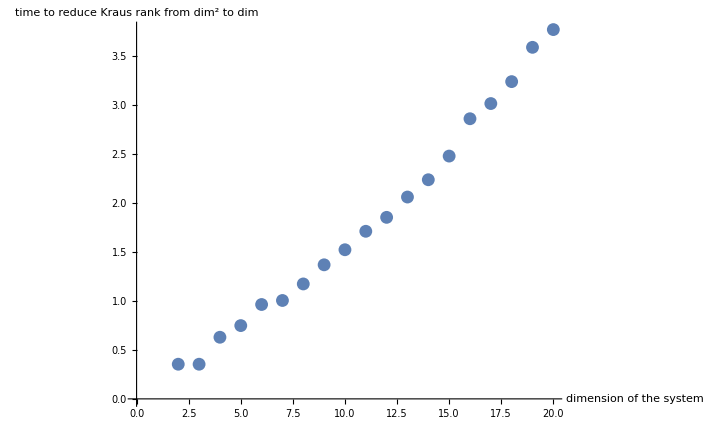

```mathematica
ListPlot[{#⟦1⟧,(#⟦2⟧)^(1/4)}&/@{{2,0.015625},{3,0.015625},{4,0.15625},{5,0.3125},{6,0.859375},{7,1.015625},{8,1.890625},{9,3.5},{10,5.359375},{11,8.546875},{12,11.765625},{13,17.984375},{14,24.984375},{15,37.65625},{16,66.734375},{17,82.421875},{18,109.765625},{19,165.5},{20,201.515625}},AxesLabel->{"dimension of the system","time to reduce Kraus rank from dim^2 to dim"}]
```

```mathematica
Fit[{#⟦1⟧,#⟦2⟧}&/@{{2,0.015625},{3,0.015625},{4,0.15625},{5,0.3125},{6,0.859375},{7,1.015625},{8,1.890625},{9,3.5},{10,5.359375},{11,8.546875},{12,11.765625},{13,17.984375},{14,24.984375},{15,37.65625},{16,66.734375},{17,82.421875},{18,109.765625},{19,165.5},{20,201.515625}},{dim^4},dim]
```

0.00114016 dim^4

```mathematica
0.0011401617008346453 dim^4/3600/.dim->100
```

31.6712

The algorithm scales more or less as the number of Choi matrix of the channel, so as d^4, approximatelly 0.00114016 d^4. 
For d=20, the timing of a single spoofing is of the order of 200 s.
Therefore, we could go with dimension as high as d=100, in time around 31h.

```mathematica
0.0011401617008346453 32^4/3600
```

0.332096

#### Testing

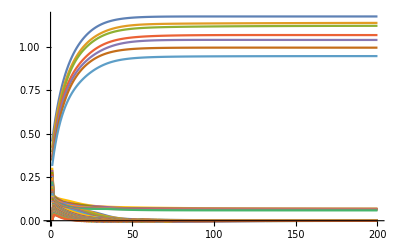
If we try to go to lower rank than d, even by one, the algorithm does not converge, but some eigenvalues stabilize:  -Graphics-

#### Eigenvalues convergence for Sinkhorn-like algorithm

We take the data from the algorithm for reducing rank for d=20 dimensional generic quantum channel.

```mathematica
(*Using MaTeX library for plots*)
<<MaTeX`
```

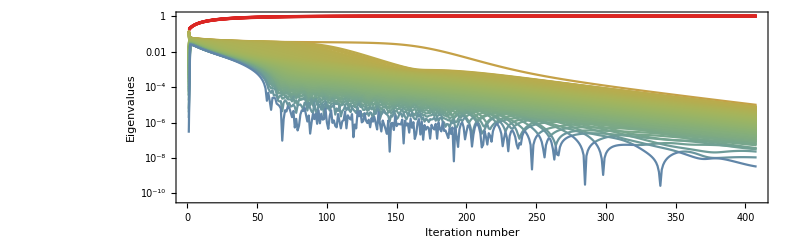

```mathematica
ListLogPlot[Abs@eigenvaluesList, Joined->True,Frame->{{True,False},{True,False}},FrameLabel->{{"Eigenvalues",None},{"Iteration number",None}},BaseStyle->Directive[{FontFamily->"LM Roman 10",FontSize->17}],PlotRange->All,ColorFunction->"Rainbow",AspectRatio->0.3,FrameStyle->Black,ImageSize->800]
```

### Analitycal algorithm for Pauli channels

Necessary definitions

```mathematica
(*Pauli matrices*)
depolarizingMatrices2Qubit=Flatten[Table[KroneckerProduct[PauliMatrix@i,PauliMatrix@j],{i,0,3},{j,0,3}],1];
(*Choi matrix of Pauli channel out of coefficients of Kraus matrices in the Pauli basis*)
vectorization[A_]:=ArrayReshape[A,{Length[A]^2,1}];
choiMatrix2Qubit[αList_]:=
Total@Table[αList⟦i⟧vectorization[depolarizingMatrices2Qubit⟦i⟧].vectorization[depolarizingMatrices2Qubit⟦i⟧]†,{i,Length@αList}];
```

First, we need to find the parametrization of such channels

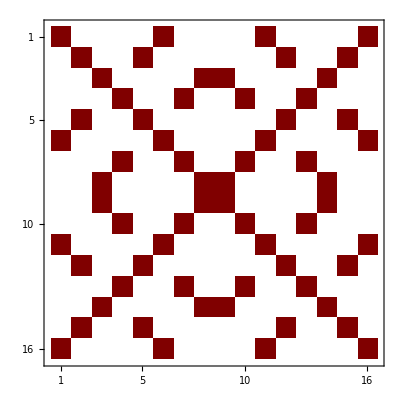

```mathematica
MatrixPlot@choiMatrix2Qubit@({{α00}, {α01}, {α02}, {α03}, {α10}, {α11}, {α12}, {α13}, {α20}, {α21}, {α22}, {α23}, {α30}, {α31}, {α32}, {α33}})
```

Observe that rows that have non-zero elements in the same column, i.e., row 1 has the same pattern as rows 6, 11, and 16. 
Therefore, by a proper choice of elements it should be doable to make them all linearly dependent!

```mathematica
choiMatrix2Qubit[({{α00}, {α01}, {α02}, {α03}, {α10}, {α11}, {α12}, {α13}, {α20}, {α21}, {α22}, {α23}, {α30}, {α31}, {α32}, {α33}})]⟦{1,6,11,16}⟧
```

{{α00+α03+α30+α33,0,0,0,0,α00-α03+α30-α33,0,0,0,0,α00+α03-α30-α33,0,0,0,0,α00-α03-α30+α33},{α00-α03+α30-α33,0,0,0,0,α00+α03+α30+α33,0,0,0,0,α00-α03-α30+α33,0,0,0,0,α00+α03-α30-α33},{α00+α03-α30-α33,0,0,0,0,α00-α03-α30+α33,0,0,0,0,α00+α03+α30+α33,0,0,0,0,α00-α03+α30-α33},{α00-α03-α30+α33,0,0,0,0,α00+α03-α30-α33,0,0,0,0,α00-α03+α30-α33,0,0,0,0,α00+α03+α30+α33}}

Note that each of the rows have exactly one element which is fixed by the spoofing condition -- the one that corresponds to a proper diagonal block. 
But, actually, it is the same element: α00+α03+α30+α33! 
What is more, all the rows are also permutations of the first one -- when we neglect zeros:

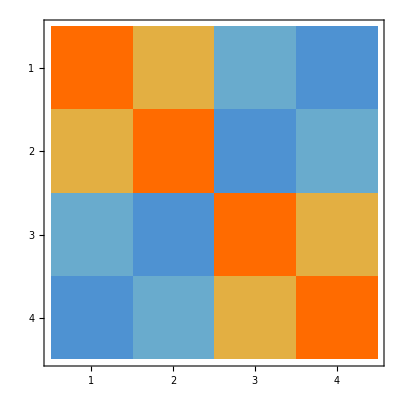

```mathematica
({{α00+α03+α30+α33, α00-α03+α30-α33, α00+α03-α30-α33, α00-α03-α30+α33}, {α00-α03+α30-α33, α00+α03+α30+α33, α00-α03-α30+α33, α00+α03-α30-α33}, {α00+α03-α30-α33, α00-α03-α30+α33, α00+α03+α30+α33, α00-α03+α30-α33}, {α00-α03-α30+α33, α00+α03-α30-α33, α00-α03+α30-α33, α00+α03+α30+α33}})/.MapThread[#1->#2&,{{α00,α03,α30,α33},RandomReal[1,{4}]}]//MatrixPlot
```

Since there are four degrees of freedom, it is possible we can just make any element an arbitrary number. 
However, since all of αs belong to [0,1], with the sum α00+α03+α30+α33<=1, there are some conditions. 
Nonetheless, suppose we choose all αs to be equal to 1/4 -- from the spoofing perspective, it means setting the diagonal part to be 1s, while one of α = 1 - Σ_restα.

```mathematica
({{α00+α03+α30+α33, α00-α03+α30-α33, α00+α03-α30-α33, α00-α03-α30+α33}, {α00-α03+α30-α33, α00+α03+α30+α33, α00-α03-α30+α33, α00+α03-α30-α33}, {α00+α03-α30-α33, α00-α03-α30+α33, α00+α03+α30+α33, α00-α03+α30-α33}, {α00-α03-α30+α33, α00+α03-α30-α33, α00-α03+α30-α33, α00+α03+α30+α33}})/.α33->1-α00-α03-α30
```

(1 | -1+2 α00+2 α30 | -1+2 α00+2 α03 | 1-2 α03-2 α30
-1+2 α00+2 α30 | 1 | 1-2 α03-2 α30 | -1+2 α00+2 α03
-1+2 α00+2 α03 | 1-2 α03-2 α30 | 1 | -1+2 α00+2 α30
1-2 α03-2 α30 | -1+2 α00+2 α03 | -1+2 α00+2 α30 | 1)

Now, we wish to explore the minimal rank of this matrix as we change α00, α03, and α30. 
For example, could we set all of the elements to be equal to 1?

```mathematica
FindInstance[-1+2 α00+2 α30==1∧-1+2 α00+2 α03==1∧1-2 α03-2 α30==1,{α00,α03,α30}]
```

{{α00→1,α03→0,α30→0}}

Then, we obtain a rank 1 matrix.

```mathematica
({{α00+α03+α30+α33, α00-α03+α30-α33, α00+α03-α30-α33, α00-α03-α30+α33}, {α00-α03+α30-α33, α00+α03+α30+α33, α00-α03-α30+α33, α00+α03-α30-α33}, {α00+α03-α30-α33, α00-α03-α30+α33, α00+α03+α30+α33, α00-α03+α30-α33}, {α00-α03-α30+α33, α00+α03-α30-α33, α00-α03+α30-α33, α00+α03+α30+α33}})/.{α00->1,α03->0,α30->0,α33->0}
```

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)

Actually, any of these values can be set to be 1 and the rank is still 1

```mathematica
({{α00+α03+α30+α33, α00-α03+α30-α33, α00+α03-α30-α33, α00-α03-α30+α33}, {α00-α03+α30-α33, α00+α03+α30+α33, α00-α03-α30+α33, α00+α03-α30-α33}, {α00+α03-α30-α33, α00-α03-α30+α33, α00+α03+α30+α33, α00-α03+α30-α33}, {α00-α03-α30+α33, α00+α03-α30-α33, α00-α03+α30-α33, α00+α03+α30+α33}})/.{α00->0,α03->1,α30->0,α33->0}
```

(1 | -1 | 1 | -1
-1 | 1 | -1 | 1
1 | -1 | 1 | -1
-1 | 1 | -1 | 1)

As such, this result proves that by type-II Pauli spoofing it is possible to spoof some Pauli channels, but we’re looking for more generality.
Therefore, we set α00+α03+α30+α33 == β with any parameter β, which transforms the matrix to the form

```mathematica
({{α00+α03+α30+α33, α00-α03+α30-α33, α00+α03-α30-α33, α00-α03-α30+α33}, {α00-α03+α30-α33, α00+α03+α30+α33, α00-α03-α30+α33, α00+α03-α30-α33}, {α00+α03-α30-α33, α00-α03-α30+α33, α00+α03+α30+α33, α00-α03+α30-α33}, {α00-α03-α30+α33, α00+α03-α30-α33, α00-α03+α30-α33, α00+α03+α30+α33}})/.α33->β-α00-α03-α30
```

(β | 2 α00+2 α30-β | 2 α00+2 α03-β | -2 α03-2 α30+β
2 α00+2 α30-β | β | -2 α03-2 α30+β | 2 α00+2 α03-β
2 α00+2 α03-β | -2 α03-2 α30+β | β | 2 α00+2 α30-β
-2 α03-2 α30+β | 2 α00+2 α03-β | 2 α00+2 α30-β | β)

Again, we wish to find all elements that are the same, if we set α00 = β, we obtain

```mathematica
({{α00+α03+α30+α33, α00-α03+α30-α33, α00+α03-α30-α33, α00-α03-α30+α33}, {α00-α03+α30-α33, α00+α03+α30+α33, α00-α03-α30+α33, α00+α03-α30-α33}, {α00+α03-α30-α33, α00-α03-α30+α33, α00+α03+α30+α33, α00-α03+α30-α33}, {α00-α03-α30+α33, α00+α03-α30-α33, α00-α03+α30-α33, α00+α03+α30+α33}})/.{α00->β,α03->0,α30->0,α33->0}
```

(β | β | β | β
β | β | β | β
β | β | β | β
β | β | β | β)

This might have worked because of the choice of the first row, which is special in the sense that α00 is always positive in all elements of the Choi matrix. 
If we choose {2,5,12,15} rows and remove zeros

```mathematica
Pick[choiMatrix2Qubit[({{α00}, {α01}, {α02}, {α03}, {α10}, {α11}, {α12}, {α13}, {α20}, {α21}, {α22}, {α23}, {α30}, {α31}, {α32}, {α33}})]⟦{2,5,12,15}⟧,Table[{False,True,False,False,True,False,False,False,False,False,False,True,False,False,True,False},{4}]]
```

(α01+α02+α31+α32 | α01-α02+α31-α32 | α01+α02-α31-α32 | α01-α02-α31+α32
α01-α02+α31-α32 | α01+α02+α31+α32 | α01-α02-α31+α32 | α01+α02-α31-α32
α01+α02-α31-α32 | α01-α02-α31+α32 | α01+α02+α31+α32 | α01-α02+α31-α32
α01-α02-α31+α32 | α01+α02-α31-α32 | α01-α02+α31-α32 | α01+α02+α31+α32)

But then again α01 enters always in a positive fashion, so the same procedure will work! 
The same with α10

```mathematica
choiMatrix2Qubit[({{α00}, {α01}, {α02}, {α03}, {α10}, {α11}, {α12}, {α13}, {α20}, {α21}, {α22}, {α23}, {α30}, {α31}, {α32}, {α33}})]⟦{3,8,9,14}⟧
```

{{0,0,α10+α13+α20+α23,0,0,0,0,α10-α13+α20-α23,α10+α13-α20-α23,0,0,0,0,α10-α13-α20+α23,0,0},{0,0,α10-α13+α20-α23,0,0,0,0,α10+α13+α20+α23,α10-α13-α20+α23,0,0,0,0,α10+α13-α20-α23,0,0},{0,0,α10+α13-α20-α23,0,0,0,0,α10-α13-α20+α23,α10+α13+α20+α23,0,0,0,0,α10-α13+α20-α23,0,0},{0,0,α10-α13-α20+α23,0,0,0,0,α10+α13-α20-α23,α10-α13+α20-α23,0,0,0,0,α10+α13+α20+α23,0,0}}

and α11

```mathematica
choiMatrix2Qubit[({{α00}, {α01}, {α02}, {α03}, {α10}, {α11}, {α12}, {α13}, {α20}, {α21}, {α22}, {α23}, {α30}, {α31}, {α32}, {α33}})]⟦{4,7,10,13}⟧
```

{{0,0,0,α11+α12+α21+α22,0,0,α11-α12+α21-α22,0,0,α11+α12-α21-α22,0,0,α11-α12-α21+α22,0,0,0},{0,0,0,α11-α12+α21-α22,0,0,α11+α12+α21+α22,0,0,α11-α12-α21+α22,0,0,α11+α12-α21-α22,0,0,0},{0,0,0,α11+α12-α21-α22,0,0,α11-α12-α21+α22,0,0,α11+α12+α21+α22,0,0,α11-α12+α21-α22,0,0,0},{0,0,0,α11-α12-α21+α22,0,0,α11+α12-α21-α22,0,0,α11-α12+α21-α22,0,0,α11+α12+α21+α22,0,0,0}}

Why is that the case? This stems from 1 and σ_x parameters -- both of them enter 1-qubit Choi matrix in a positive fashion as well.

Is there a simple rule how to join these coefficients into groups in the case of higher number of qubits?
Let us start by describing the group number for 2-qubit case

```mathematica
({{α00}, {α01}, {α02}, {α03}, {α10}, {α11}, {α12}, {α13}, {α20}, {α21}, {α22}, {α23}, {α30}, {α31}, {α32}, {α33}})==({{1}, {2}, {2}, {1}, {3}, {4}, {4}, {3}, {3}, {4}, {4}, {3}, {1}, {2}, {2}, {1}})
```

is seems that {0,3} and {1,2} both go together in a different fashion.
Probably such vector can be written as

```mathematica
KroneckerProduct[{{a,b,b,a}},{{c,d,d,c}}]ᵀ/.{a c->1,a d->2,b c->3,b d->4}//MatrixForm
```

(1
2
2
1
3
4
4
3
3
4
4
3
1
2
2
1)

so we have found a recipe!